```mathematica
SetOptions[{ListPlot,Plot,LogLinearPlot,ListLogPlot},{PlotRange->All,Frame->True,FrameStyle->Thick,PlotStyle->Thick,BaseStyle->{FontFamily->"Gill Sans MT",FontSize->22},FrameTicks-> {{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{"DAC","ADC"},Axes-> False,PlotLabel->"",ImageSize-> 800}]; (* set the options for the plots *)
```

```mathematica
dir="E:/Dokumente/gitlab/UEIO800/python_interface/";
```

```mathematica
fina=FileNames[dir<>"demo_analog_loopback_data_128.dat"];
```

```mathematica
data1=Table[Import[fina⟦xx⟧,{"Data",{All},{2,3}}],{xx,1,Length[fina]}];
data2=Table[Import[fina⟦xx⟧,{"Data",{All},{2,4}}],{xx,1,Length[fina]}];
```

Import::noelem: The Import element "4" is not present when importing as "Table".

```mathematica
Dimensions[data1]
```

{1,513,2}

```mathematica
aplot = ListPlot[data1⟦All⟧,PlotRange-> All,Joined-> True];
```

```mathematica
bplot = ListPlot[data2⟦All⟧,PlotRange-> All,Joined-> True, PlotStyle->{Thick, Red}];
```

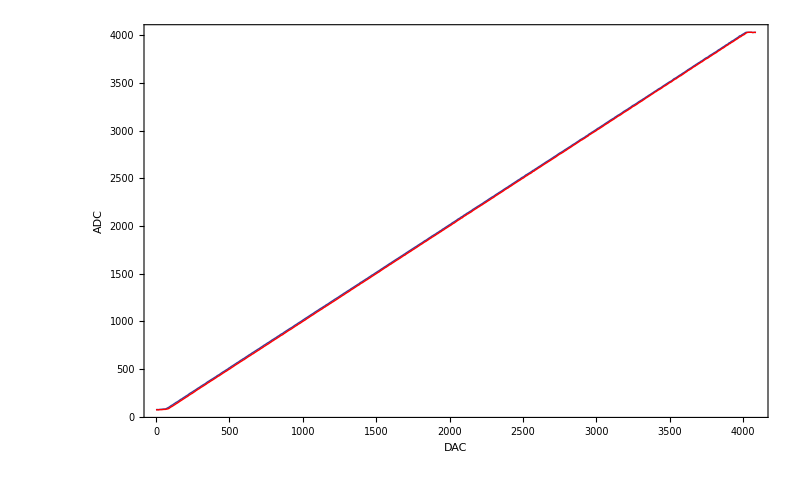

```mathematica
Show[aplot, bplot]
```